```mathematica
transform[TProduct[{{0, 0}, {0, 1}}, σI, σI], UtoGE] // TrigToExp // FullSimplify // MatrixForm
```

(1/2-(d e ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
0 | 1/2-(d e ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0
0 | 0 | 1/2-(d e ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
0 | 0 | 0 | 1/2-(d e ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
(h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -1/2-(d e ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
0 | (h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -1/2-(d e ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0
0 | 0 | (h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -1/2-(d e ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
0 | 0 | 0 | (h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -1/2-(d e ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)))

```mathematica
Simplify[1/2-(d e ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)), h == h*ϵ/√(h^2 Vt^2+d^2 e^2 ΔE^2)]
```

```mathematica
(-A h √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 d e ΔE √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 h γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ+d e h ΔE (A-2 B0 (2 γn+γe (2+Δγ))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) // Apart
```

(d e ΔE)/(2 h)+(A d e ΔE)/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2))-(B0 d e γe ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))-(B0 d e γn ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))-(B0 d e γe ΔE Δγ)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2))+1/8 (-A+2 B0 γe Δγ)

```mathematica
printWithBasis[transform[H, UtoGE] // TrigToExp // FullSimplify, basisGE]
```

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | ((A h √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 d e ΔE √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 h γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ-d e h ΔE (A+2 B0 (-2 γn+γe (2+Δγ))))/(√(h^2 Vt^2+d^2 e^2 ΔE^2))+4 d e Eac Cos[t νE])/(8 h) | (Bac d e γn ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac d e γe ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | (-4 Vt √(h^2 Vt^2+d^2 e^2 ΔE^2)+h Vt (A+2 B0 (-2 γn+γe (2+Δγ))))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac h Vt γn Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Bac h Vt γe Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|g↓⇑> | (Bac d e γn ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | ((-A h √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 d e ΔE √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 h γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ+d e h ΔE (A-2 B0 (2 (γe+γn)+γe Δγ)))/(√(h^2 Vt^2+d^2 e^2 ΔE^2))+4 d e Eac Cos[t νE])/(8 h) | 1/4 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | -(Bac d e γe ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac h Vt γn Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Vt (-A h-4 √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 h (2 (γe+γn)+γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Bac h Vt γe Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
|g↑⇓> | -(Bac d e γe ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 1/4 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | ((-A h √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 d e ΔE √(h^2 Vt^2+d^2 e^2 ΔE^2)-2 B0 h γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ+d e h ΔE (A+4 B0 (γe+γn)+2 B0 γe Δγ))/(√(h^2 Vt^2+d^2 e^2 ΔE^2))+4 d e Eac Cos[t νE])/(8 h) | (Bac d e γn ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Bac h Vt γe Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (-4 Vt √(h^2 Vt^2+d^2 e^2 ΔE^2)-h Vt (A+4 B0 (γe+γn)+2 B0 γe Δγ))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac h Vt γn Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
|g↑⇑> | 0 | -(Bac d e γe ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Bac d e γn ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | ((A h √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 d e ΔE √(h^2 Vt^2+d^2 e^2 ΔE^2)-2 B0 h γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ-d e h ΔE (A-2 B0 (-2 γn+γe (2+Δγ))))/(√(h^2 Vt^2+d^2 e^2 ΔE^2))+4 d e Eac Cos[t νE])/(8 h) | 0 | (Bac h Vt γe Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac h Vt γn Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (-4 Vt √(h^2 Vt^2+d^2 e^2 ΔE^2)+h Vt (A-2 B0 (-2 γn+γe (2+Δγ))))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2))
|e↓⇓> | -(Vt (A h+4 √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 h (-2 γn+γe (2+Δγ))))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Bac h Vt γn Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac h Vt γe Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | -((A h √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 d e ΔE √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 h γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ+d e h ΔE (A+2 B0 (-2 γn+γe (2+Δγ))))/(√(h^2 Vt^2+d^2 e^2 ΔE^2))+4 d e Eac Cos[t νE])/(8 h) | (Bac d e γn ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac d e γe ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|e↓⇑> | (Bac h Vt γn Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (-4 Vt √(h^2 Vt^2+d^2 e^2 ΔE^2)+h Vt (A-2 B0 (2 γn+γe (2+Δγ))))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac h Vt γe Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Bac d e γn ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | ((A h √(h^2 Vt^2+d^2 e^2 ΔE^2)-4 d e ΔE √(h^2 Vt^2+d^2 e^2 ΔE^2)-2 B0 h γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ+d e h ΔE (A-2 B0 (2 (γe+γn)+γe Δγ)))/(√(h^2 Vt^2+d^2 e^2 ΔE^2))-4 d e Eac Cos[t νE])/(8 h) | 1/4 A (-1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | -(Bac d e γe ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
|e↑⇓> | -(Bac h Vt γe Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (-4 Vt √(h^2 Vt^2+d^2 e^2 ΔE^2)+h Vt (A+4 B0 (γe+γn)+2 B0 γe Δγ))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Bac h Vt γn Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac d e γe ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 1/4 A (-1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | ((A h √(h^2 Vt^2+d^2 e^2 ΔE^2)-4 d e ΔE √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 h γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ+d e h ΔE (A+4 B0 (γe+γn)+2 B0 γe Δγ))/(√(h^2 Vt^2+d^2 e^2 ΔE^2))-4 d e Eac Cos[t νE])/(8 h) | (Bac d e γn ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
|e↑⇑> | 0 | -(Bac h Vt γe Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Bac h Vt γn Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Vt (-A h-4 √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 h (-2 γn+γe (2+Δγ))))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | -(Bac d e γe ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Bac d e γn ΔE Sin[2 π t νB])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -((A h √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 d e ΔE √(h^2 Vt^2+d^2 e^2 ΔE^2)-2 B0 h γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ+d e h ΔE (A-2 B0 (-2 γn+γe (2+Δγ))))/(√(h^2 Vt^2+d^2 e^2 ΔE^2))+4 d e Eac Cos[t νE])/(8 h))

```mathematica
UtoGE // MatrixForm
```

(-Sin[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0 | Cos[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0
0 | -Sin[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0 | Cos[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0
0 | 0 | -Sin[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0 | Cos[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0
0 | 0 | 0 | -Sin[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0 | Cos[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]]
-Cos[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0 | -Sin[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0
0 | -Cos[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0 | -Sin[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0
0 | 0 | -Cos[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0 | -Sin[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0
0 | 0 | 0 | -Cos[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]] | 0 | 0 | 0 | -Sin[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]])

```mathematica
printWithBasis[transform[A*TProduct[{{0, 0}, {0, 1}}, σI, σI], UtoGE] // TrigToExp // FullSimplify, basisGE]
```

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | 1/2 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | 0 | 0 | 0 | (A h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
|g↓⇑> | 0 | 1/2 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | 0 | 0 | 0 | (A h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0
|g↑⇓> | 0 | 0 | 1/2 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | 0 | 0 | 0 | (A h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|g↑⇑> | 0 | 0 | 0 | 1/2 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | 0 | 0 | 0 | (A h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
|e↓⇓> | -(A h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | 1/2 A (-1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | 0 | 0 | 0
|e↓⇑> | 0 | -(A h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | 1/2 A (-1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | 0 | 0
|e↑⇓> | 0 | 0 | -(A h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | 1/2 A (-1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | 0
|e↑⇑> | 0 | 0 | 0 | -(A h Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | 1/2 A (-1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))))

```mathematica
ϵ0
```

√(Vt^2+(d^2 e^2 ΔE^2)/h^2)

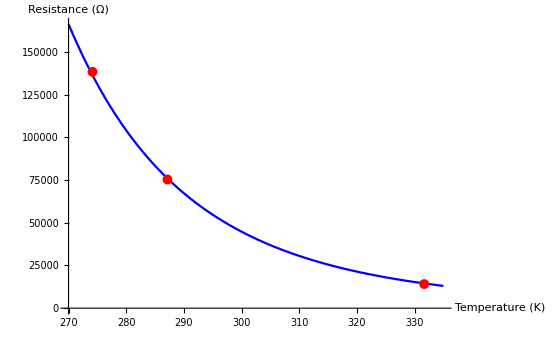

```mathematica
Ts = {274.15, 287.15, 331.65};
Rs = {138300, 75300, 14100};
Show[
Plot[61200*E^(3543.908*(1/TT - 1/292.25)), {TT, 270, 335}, PlotStyle->Blue, AxesLabel->{"Temperature (K)", "Resistance (Ω)"}],
ListPlot[Transpose[{Ts, Rs}], PlotRange->Full, PlotStyle->Red]
]
```

```mathematica
printAsPauliMatrices[U]
```

Cos[(t*ωB)/2]^2 σII + (-I/2)*Sin[t*ωB] σZI + (-I/2)*Sin[t*ωB] σIZ + (-1 + Cos[t*ωB])/2 σZZ

```mathematica
U
```

```mathematica
U = MatrixExp[ⅈ*ωB*t*(TProduct[Sz, σI] + TProduct[σI, Iz])]
ConjugateTranspose[U].SdotI.U // FullSimplify // MatrixForm
SdotI // MatrixForm
```

{{ⅇ^(ⅈ t ωB),0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,ⅇ^(-ⅈ t ωB)}}

(1/4 | 0 | 0 | 0
0 | -1/4 | 1/2 | 0
0 | 1/2 | -1/4 | 0
0 | 0 | 0 | 1/4)

(1/4 | 0 | 0 | 0
0 | -1/4 | 1/2 | 0
0 | 1/2 | -1/4 | 0
0 | 0 | 0 | 1/4)

```mathematica
σI + ⅈ*q*σY
ConjugateTranspose[%].% // MatrixForm
```

{{1,q},{-q,1}}

```mathematica
Square[3]
```

□3

```mathematica
Sqrt[T^2 // FullSimplify]
```

(√(1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))))/(√2)

```mathematica
T =  Sqrt[(-Sin[ArcTan[-((e*ΔE*d)/h), Vt]/2])^2 // TrigToExp // FullSimplify] // FullSimplify
((T - Conjugate[T])// FullSimplify) /. {ΔE -> 0, Vt -> 1, h -> 1}  // FullSimplify
((T - Conjugate[T]) // TrigToExp // FullSimplify) /. {ΔE -> 0, Vt -> 1, h -> 1} // FullSimplify
((T - Conjugate[T]) // TrigToExp) /. {ΔE -> 0, Vt -> 1, h -> 1} // FullSimplify
((T - Conjugate[T]) /. {ΔE -> 0, Vt -> 1, h -> 1}// FullSimplify)
```

(√(1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))))/(√2)

0

0

0

«1 more identical outputs»

```mathematica
Q = (1*σI + ⅈ*T*σY);

setVariables[]
clearVariables[]
T =  -Sin[ArcTan[a, b]/2];
M = σI + ⅈ*T*σY;
term = (ConjugateTranspose[M].M)[[1, 2]]

(term) /. {ΔE -> 0, Vt -> 1, h -> 1} // FullSimplify
(term // Conjugate // TrigToExp) /. {ΔE -> 0, Vt -> 1, h -> 1} // FullSimplify
```

-Sin[1/2 ArcTan[-(d e ΔE)/(2 h),Vt/2]]+Sin[1/2 Conjugate[ArcTan[-(d e ΔE)/(2 h),Vt/2]]]

0

0